## DTissue-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Wed 7 Jun 2017 10:42:11
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

There are 14 cells in the tissue.

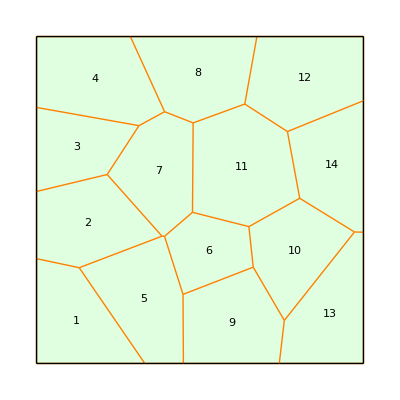

```mathematica
q=TemplateRandomSquareGrid[12, {-50, -50}, {50, 50}];
Q=Tissue2DTissue[q]; 
Print["There are ", NTissueCells[Q], " cells in the tissue."];  
ShowTissue[Q, "CellNumbers"-> True, Frame-> False, "EdgeStyles"-> Directive[Orange,Thick]]
```

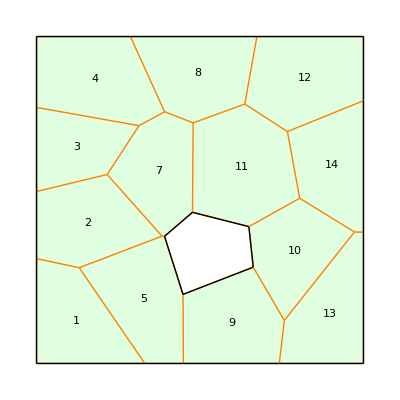

```mathematica
R=DeleteCell[Q,6];
ShowTissue[R, "CellNumbers"-> True, "EdgeStyles"-> Directive[Orange,Thick]]
```

```mathematica
Q
```

DTissue[{{-36.9454,-20.7109},{-28.392,7.79345},{-18.6559,22.7411},{-11.6177,-11.0611},{-10.8527,-11.1112},{-10.8263,27.0037},{-5.19496,-28.8689},{-2.29681,-3.76844},{-2.09254,23.588},{13.6997,29.3521},{14.9537,-8.1385},{16.283,-20.5454},{25.7877,-36.8412},{26.7426,20.9365},{30.4977,0.531599},{47.2553,-9.78779},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-9.83778},{50.,30.3671},{17.4071,50.},{-21.2979,50.},{-50.,28.3147},{-50.,2.60754},{-50.,-17.9441},{-16.8782,-50.},{-5.07878,-50.},{24.2515,-50.}},{{1,4},{1,27},{1,28},{2,3},{2,4},{2,26},{3,6},{3,25},{4,5},{5,7},{5,8},{6,9},{6,24},{7,12},{7,29},{8,9},{8,11},{9,10},{10,14},{10,23},{11,12},{11,15},{12,13},{13,16},{13,30},{14,15},{14,22},{15,16},{16,21},{17,21},{17,30},{18,22},{18,23},{19,24},{19,25},{20,27},{20,28},{21,22},{23,24},{25,26},{26,27},{28,29},{29,30}},{1→{37,3,2,36},2→{41,2,1,5,6},3→{40,6,4,8},4→{35,8,7,13,34},5→{42,15,10,9,1,3},6→{10,14,21,17,11},7→{4,5,9,11,16,12,7},8→{39,13,12,18,20},9→{43,25,23,14,15},10→{21,23,24,28,22},11→{16,17,22,26,19,18},12→{33,20,19,27,32},13→{29,24,25,31,30},14→{38,27,26,28,29}}]

```mathematica
R
```

DTissue[{{-36.9454,-20.7109},{-28.392,7.79345},{-18.6559,22.7411},{-11.6177,-11.0611},{-10.8527,-11.1112},{-10.8263,27.0037},{-5.19496,-28.8689},{-2.29681,-3.76844},{-2.09254,23.588},{13.6997,29.3521},{14.9537,-8.1385},{16.283,-20.5454},{25.7877,-36.8412},{26.7426,20.9365},{30.4977,0.531599},{47.2553,-9.78779},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-9.83778},{50.,30.3671},{17.4071,50.},{-21.2979,50.},{-50.,28.3147},{-50.,2.60754},{-50.,-17.9441},{-16.8782,-50.},{-5.07878,-50.},{24.2515,-50.}},{{1,4},{1,27},{1,28},{2,3},{2,4},{2,26},{3,6},{3,25},{4,5},{5,7},{5,8},{6,9},{6,24},{7,12},{7,29},{8,9},{8,11},{9,10},{10,14},{10,23},{11,12},{11,15},{12,13},{13,16},{13,30},{14,15},{14,22},{15,16},{16,21},{17,21},{17,30},{18,22},{18,23},{19,24},{19,25},{20,27},{20,28},{21,22},{23,24},{25,26},{26,27},{28,29},{29,30}},{1→{37,3,2,36},2→{41,2,1,5,6},3→{40,6,4,8},4→{35,8,7,13,34},5→{42,15,10,9,1,3},7→{4,5,9,11,16,12,7},8→{39,13,12,18,20},9→{43,25,23,14,15},10→{21,23,24,28,22},11→{16,17,22,26,19,18},12→{33,20,19,27,32},13→{29,24,25,31,30},14→{38,27,26,28,29}}]

```mathematica
TissueCells[R]
```

{1→{37,3,2,36},2→{41,2,1,5,6},3→{40,6,4,8},4→{35,8,7,13,34},5→{42,15,10,9,1,3},7→{4,5,9,11,16,12,7},8→{39,13,12,18,20},9→{43,25,23,14,15},10→{21,23,24,28,22},11→{16,17,22,26,19,18},12→{33,20,19,27,32},13→{29,24,25,31,30},14→{38,27,26,28,29}}